## Mathematica bevezető

```mathematica
4
```

4

```mathematica
4*3
```

12

```mathematica
c=5+8
```

13

```mathematica
c
```

13

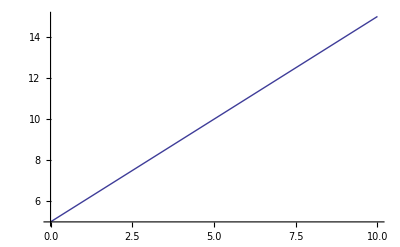

```mathematica
Plot[x+5,{x,0,10}]
```

```mathematica
f[x_]=x^2
```

x^2

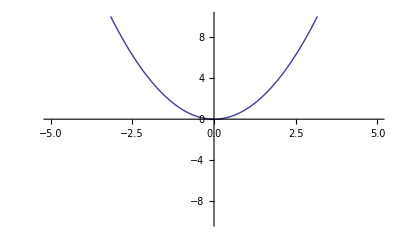

```mathematica
Plot[{f[x]},{x,-5,5},PlotRange->10]
```

```mathematica
f'[x]
```

2 x

## elemi függvények deriváltja

## (x^α)’= α x^(α-1)

```mathematica
f[x_]=x^4
```

x^4

```mathematica
f'[x]
```

4 x^3

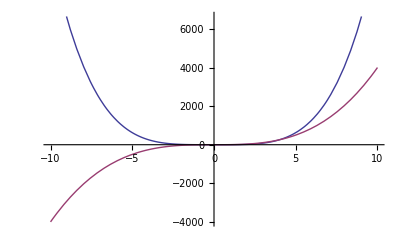

```mathematica
Plot[{f[x],f'[x]},{x,-10,10}]
```

```mathematica
f[x_]=x^3
```

x^3

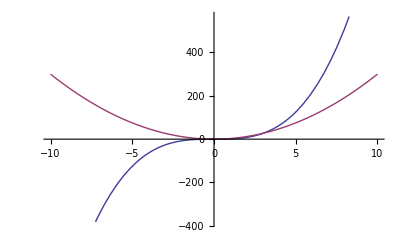

```mathematica
Plot[{f[x],f'[x]},{x,-10,10}]
```

```mathematica
f[x_]=x^2
```

x^2

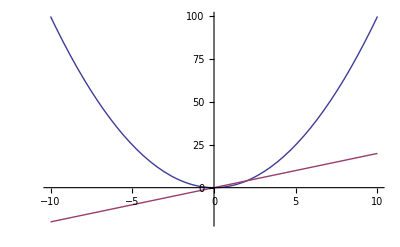

```mathematica
Plot[{f[x],f'[x]},{x,-10,10}]
```

```mathematica
f[x_]=x
```

x

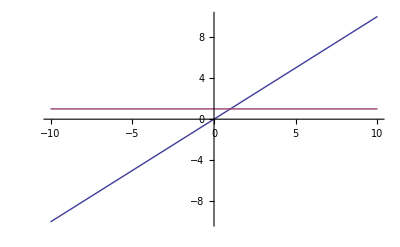

```mathematica
Plot[{f[x],f'[x]},{x,-10,10}]
```

```mathematica
f[x_]=x^4
```

x^4

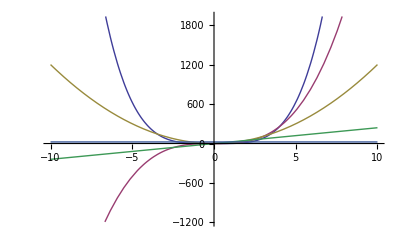

```mathematica
Plot[{f[x],f'[x],f''[x],f'''[x],f''''[x]},{x,-10,10},PlotStyle->Thick]
```

## trigonometrikus függvények

```mathematica
f[x_]=Sin[x]
```

Sin[x]

```mathematica
f'[x]
```

Cos[x]

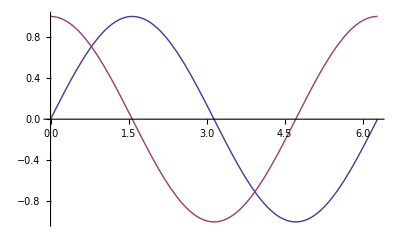

```mathematica
Plot[{f[x],f'[x]},{x,0,2 Pi}]
```

```mathematica
f[x_]=Cos[x]
```

Cos[x]

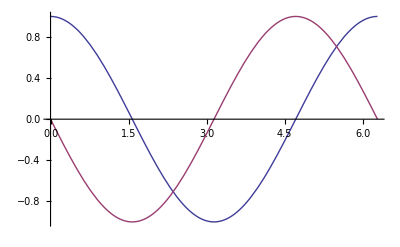

```mathematica
Plot[{f[x],f'[x]},{x,0,2 Pi}]
```

```mathematica
f[x_]=Sin[x]
```

Sin[x]

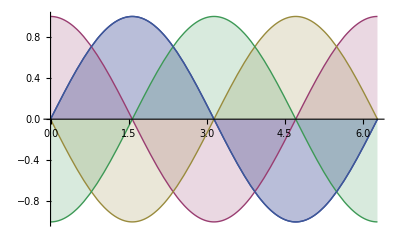

```mathematica
Plot[{f[x],f'[x],f''[x],f'''[x],f''''[x]},{x,0,2 Pi},Filling->Axis]
```

## exponenciális

```mathematica
f[x_]=10^x
```

10^x

```mathematica
f'[x]
```

10^x Log[10]

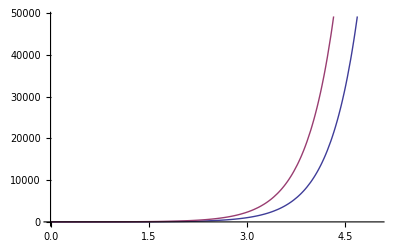

```mathematica
Plot[{f[x],f'[x]},{x,0,5}]
```

```mathematica
f[x_]=E^x
```

ⅇ^x

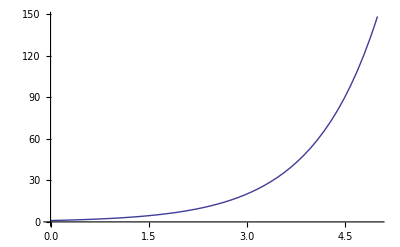

```mathematica
Plot[f[x],{x,0,5}]
```

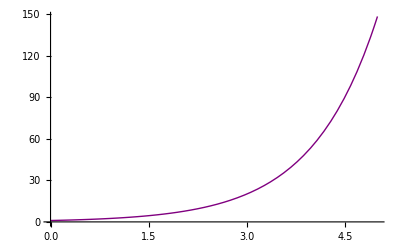

```mathematica
Plot[f'[x],{x,0,5},PlotStyle->Purple]
```

## logaritmus

```mathematica
f[x_]=Log[10,x]
```

Log[x]/Log[10]

```mathematica
f'[x]
```

1/(x Log[10])

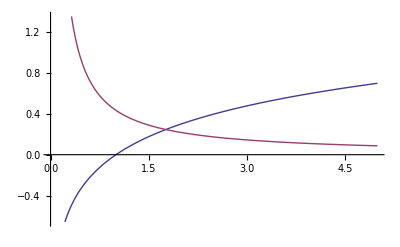

```mathematica
Plot[{f[x],f'[x]},{x,0,5}]
```

```mathematica
Log[10.]
```

2.30259

```mathematica
Log[100.]
```

4.60517

```mathematica
Log[100.]/Log[10.]
```

2.

```mathematica
Log[10,100]
```

2